## 365 Photo project

### Import

```mathematica
files=FileNames["*.jpg","~/Dev/365/"];
```

```mathematica
Length[files]
```

365

```mathematica
images=ImageResize[Import[#],{1000}]&/@files;
```

```mathematica
exif=Import[#,{"JPEG","Exif"}]&/@files;
```

```mathematica
images[[1]]
```

-Graphics-

```mathematica
imagesAndData=Transpose[{images,exif,FileNameTake/@files}];
```

### Sorting

```mathematica
ClearAll[time];
time[im_]:=Which[
KeyExistsQ[im[[2]],"DateTimeOriginal"],AbsoluteTime[im[[2]]["DateTimeOriginal"]],
KeyExistsQ[im[[2]],"DateTime"],AbsoluteTime[im[[2]]["DateTime"]],
StringMatchQ[im[[3]],"IMG_"~~DigitCharacter..~~"_"~~(DigitCharacter|"_")..~~".jpg"],AbsoluteTime[StringCases[im[[3]],"IMG_"~~date:DigitCharacter..~~"_"~~(DigitCharacter|"_")..~~".jpg":>date][[1]]],
True,None]
```

```mathematica
Position[time/@imagesAndData,None]
```

KeyExistsQ::invrl: The argument None is not a valid Association or a list of rules.

{}

```mathematica
Extract[imagesAndData,%]
```

{}

```mathematica
imagesAndData2=Map[Append[#,time[#]]&,imagesAndData];
```

KeyExistsQ::invrl: The argument None is not a valid Association or a list of rules.

```mathematica
imagesAndData3=SortBy[imagesAndData2,Last];
```

### Preparation

```mathematica
imagesAndDataTiny=Map[Join[{ImageResize[#[[1]],{100}]},#[[2;;]]]&,imagesAndData3];
```

```mathematica
Sqrt[365.]
```

19.105

```mathematica
pimdata=Partition[imagesAndDataTiny[[All,1]],UpTo[20]];
```

### Presentations

#### Grid

```mathematica
Grid[pimdata,Spacings->{0,0},ItemSize->3]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

#### Dominant colors

```mathematica
dominantColors=DominantColors[#[[1]],1]&/@imagesAndDataTiny;
```

```mathematica
lineWidth=0.05;
```

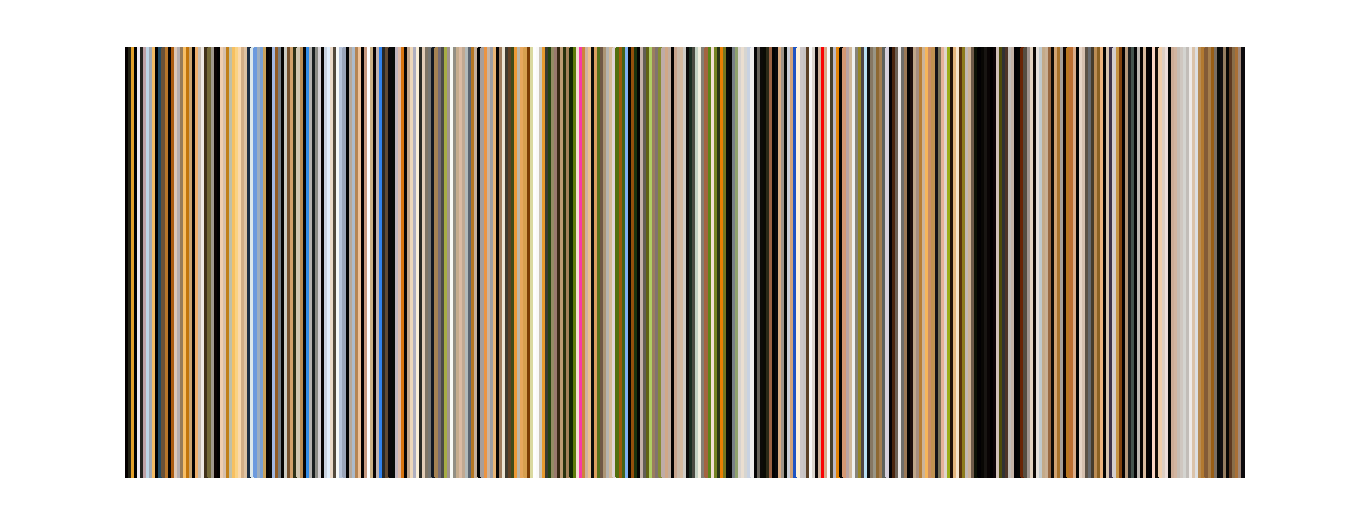

```mathematica
Graphics@Table[{FaceForm[dominantColors[[i]]],Rectangle[{i*lineWidth,0},{(i+1)*lineWidth,7}]},{i,Length[imagesAndDataTiny]}]
```

### Multiple Dominant Colors

```mathematica
multipleDominantColors=DominantColors[#[[1]],15,{"Color","Coverage"}]&/@imagesAndDataTiny[[;;]];
```

```mathematica
multipleDominantColorsSorted=SortBy[#,ColorConvert[#[[1]],"HSB"][[1]]&]&/@multipleDominantColors;
```

```mathematica
height=7;
```

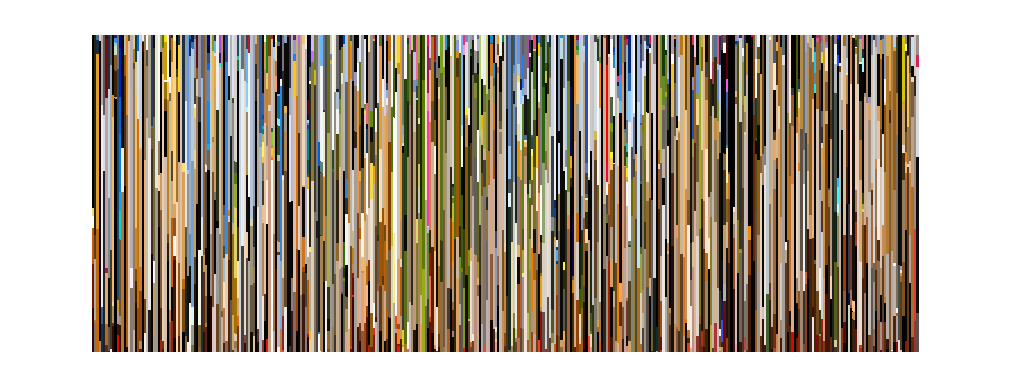

```mathematica
Graphics@Table[{Module[{colors=Transpose[{multipleDominantColorsSorted[[i]][[All,1]],Accumulate@(#/Total[#]&[multipleDominantColorsSorted[[i]][[All,2]]])}]},Table[{FaceForm[colors[[ci]][[1]]],Rectangle[{i*lineWidth,(If[ci===1,0,colors[[ci-1]][[2]]])*height},{(i+1)*lineWidth,(colors[[ci]][[2]])*height}]},{ci,Length[colors]}]]},{i,Length[multipleDominantColorsSorted]}]
```

### Hue

```mathematica
ClearAll[extractPixelColumn];
extractPixelColumn[im_]:=SortBy[#,ColorConvert[#,"HSB"][[1]]&]&/@(RGBColor/@Join@@ImageData[ImageResize[im[[1]],{1,300},Resampling->"Gaussian"]])
```

```mathematica
pixelcolumns=extractPixelColumn/@imagesAndData3[[;;]];
```

```mathematica
ClearAll[smoothPixelColumn];
smoothPixelColumn[pc_]:=Module[{cc=(ColorConvert[#,"HSB"]&/@pc)},
BlockMap[Hue[#[[4,1]],#[[4,2]],Mean[#[[All,3]]]]&,cc,7,1]
]
```

```mathematica
Image[Transpose[smoothPixelColumn/@pixelcolumns]]
```

-Graphics-

```mathematica
Export["~/Dropbox/temp/365Colors.png",ImageResize[Image[Transpose[smoothPixelColumn/@pixelcolumns]],1000,Resampling->"NearestLeft"]]
```

ImageResize::cscycl: ImageResize does not support images with a cyclic Hue channel. Assuming Automatic color space instead.

~/Dropbox/temp/365Colors.png

#### Summary Dominant Colors

```mathematica
ImageCollage
```

```mathematica
imcollages=ImageCollage[#,"Stretch",Method->"Grid"]&/@Partition[imagesAndDataTiny[[All,1]],UpTo[9]];
```

```mathematica
imcollages//Length
```

41

```mathematica
imcollagesDominant=DominantColors[#,1]&/@imcollages
```

{{RGBColor[0.012216870319293298, 0.006265781667301916, 0.005642884350297253]},{RGBColor[0.01524958100193179, 0.0069734427642049865, 0.005576699839673492]},{RGBColor[0.6109308038886209, 0.5726762689351902, 0.5048696225550716]},{RGBColor[0.8264278420402503, 0.7356383156048789, 0.6546222213002968]},{RGBColor[0.9139571785893502, 0.8044940180319399, 0.6775413767780047]},{RGBColor[0.0255489933527003, 0.019195883655706052, 0.012670941149994026]},{RGBColor[0.6659646008118949, 0.6973651781022449, 0.7192644865667417]},{RGBColor[0.9104867715632486, 0.8402317194567336, 0.7729342618424141]},{RGBColor[0.7280723667059026, 0.5498223348449404, 0.3728553243205444]},{RGBColor[0.03198779606971321, 0.02330581070427587, 0.03214666928019068]},{RGBColor[0.7830464376336825, 0.6770167518817636, 0.5791336760073945]},{RGBColor[0.291517316241225, 0.28589229608522654, 0.2720803723946055]},{RGBColor[0.7312564710222563, 0.6391207464344505, 0.5596952085854772]},{RGBColor[0.7790915059814985, 0.6974033689404869, 0.6115991396340826]},{RGBColor[0.9822229641574928, 0.9836692877018544, 0.9812186559844222]},{RGBColor[0.7044452376685015, 0.5847490955407225, 0.44899787855582546]},{RGBColor[0.9461473489329045, 0.870986721577848, 0.8105038768884251]},{RGBColor[0.7429647998923722, 0.6066446756682872, 0.4574349788097581]},{RGBColor[0.3853904150233994, 0.4177976602111007, 0.08114609862608146]},{RGBColor[0.8195611874313798, 0.6767989530542563, 0.5574985049870519]},{RGBColor[0.8042924274234455, 0.7988739041841122, 0.777298612225173]},{RGBColor[0.4713650829282697, 0.2989735501294355, 0.20951157115325464]},{RGBColor[0.8389496456638125, 0.8328992046512512, 0.8179605872983291]},{RGBColor[0.022949166622618703, 0.02196856037434152, 0.025032666856387584]},{RGBColor[0.7965995620449764, 0.7809568530607089, 0.7911251665067707]},{RGBColor[0.03121094636743093, 0.020748966665273982, 0.021331767819467776]},{RGBColor[0.9725964497712954, 0.9735915419398374, 0.970610972773181]},{RGBColor[0.015516769492440255, 0.014436885465152012, 0.021514774786509965]},{RGBColor[0.6733638096031792, 0.5656255244836539, 0.454096443313516]},{RGBColor[0.898590117823255, 0.8170113717126861, 0.6967020403788141]},{RGBColor[0.7389667745956338, 0.7000760864320418, 0.671549774053828]},{RGBColor[0.01299671531185983, 0.008103074253872525, 0.00751122355876251]},{RGBColor[0.028054904398003826, 0.025067054965604386, 0.0223490538654459]},{RGBColor[0.7380288805371941, 0.6374734329747486, 0.5250900556246159]},{RGBColor[0.018102546439772955, 0.010345377594058512, 0.011036125842964827]},{RGBColor[0.752120842338498, 0.5556535517298659, 0.23775572235264952]},{RGBColor[0.034446293721905136, 0.026901312799344643, 0.026675889141487975]},{RGBColor[0.01842514295503535, 0.014612573885993357, 0.010152609573853036]},{RGBColor[0.8351461265118992, 0.830967820143396, 0.817239742301628]},{RGBColor[0.670889563383449, 0.5140410447143987, 0.3214189043098593]},{RGBColor[0.1993456773111988, 0.20059508747582333, 0.20067648472113103]}}

```mathematica
ImageResize[Image[Transpose@imcollagesDominant],{200,100},Resampling->"Nearest"]
```

-Graphics-

### Location

```mathematica
positions=Function[im,If[AssociationQ[im[[2]]]&&KeyExistsQ[im[[2]],"GPSLatitude"],GeoPosition[{im[[2]]["GPSLatitude"],im[[2]]["GPSLongitude"]}],Missing[]]]/@imagesAndDataTiny[[;;]];
```

```mathematica
GeoGraphics[GeoMarker/@DeleteMissing@positions,GeoRange->"World",ImageSize->1500]
```

#### Time of day

```mathematica
ClearAll[timeOfDay];
timeOfDay[im_]:=Which[
KeyExistsQ[im[[2]],"DateTimeOriginal"],TimeObject[im[[2]]["DateTimeOriginal"]],
KeyExistsQ[im[[2]],"DateTime"],TimeObject[im[[2]]["DateTime"]],
True,Missing[]]
```

```mathematica
timeOfDay[imagesAndDataTiny[[1]]]-TimeObject[{0,0,0}]
```

22.4036 h

```mathematica
timeOfDayData=Select[Map[{DateObject[#[[4]]],timeOfDay[#]-TimeObject[{0,0,0}]}&,imagesAndDataTiny[[;;]]],FreeQ[#,Missing]&]
```

KeyExistsQ::invrl: The argument None is not a valid Association or a list of rules.

{{Fri 30 Dec 2016 22:24:13GMT+1.,22.4036 h},{Sun 1 Jan 2017 14:59:45GMT+1.,14.9958 h},{Mon 2 Jan 2017 22:32:24GMT+1.,22.54 h},{Tue 3 Jan 2017 21:01:37GMT+1.,21.0269 h},{Wed 4 Jan 2017 21:27:37GMT+1.,21.4603 h},{Thu 5 Jan 2017 21:26:42GMT+1.,21.445 h},{Fri 6 Jan 2017 12:53:26GMT+1.,12.8906 h},{Sat 7 Jan 2017 12:52:59GMT+1.,12.8831 h},{Sun 8 Jan 2017 14:58:32GMT+1.,14.9756 h},{Mon 9 Jan 2017 21:06:27GMT+1.,21.1075 h},{Tue 10 Jan 2017 20:44:29GMT+1.,20.7414 h},{Wed 11 Jan 2017 21:34:02GMT+1.,21.5672 h},{Thu 12 Jan 2017 20:05:15GMT+1.,20.0875 h},314,{Tue 19 Dec 2017 22:11:34GMT+1.,22.1928 h},{Wed 20 Dec 2017 17:18:32GMT+1.,17.3089 h},{Thu 21 Dec 2017 09:17:47GMT+1.,9.29639 h},{Fri 22 Dec 2017 18:24:33GMT+1.,18.4092 h},{Sat 23 Dec 2017 13:03:38GMT+1.,13.0606 h},{Sun 24 Dec 2017 21:37:18GMT+1.,21.6217 h},{Mon 25 Dec 2017 18:16:32GMT+1.,18.2756 h},{Tue 26 Dec 2017 17:27:37GMT+1.,17.4603 h},{Wed 27 Dec 2017 18:37:10GMT+1.,18.6194 h},{Thu 28 Dec 2017 18:16:47GMT+1.,18.2797 h},{Fri 29 Dec 2017 09:54:22GMT+1.,9.90611 h},{Sat 30 Dec 2017 15:58:37GMT+1.,15.9769 h},{Sun 31 Dec 2017 17:40:56GMT+1.,17.6822 h}}
 |  |  |  |

```mathematica
averageDayTime=Map[Mean[QuantityMagnitude/@#[[All,2]]]&,GroupBy[Map[{DateValue[#[[1]],"ISOWeekDay"],#[[2]]}&,timeOfDayData],#[[1]]<6&]]
```

<|True→18.6633,False→15.6146|>

```mathematica
{averageWeekDay,averageWeekend}={averageDayTime[True],averageDayTime[False]}
```

{18.6633,15.6146}

```mathematica
weekendColor=Lighter@Orange;
weekDayColor=Lighter@Blue;
```

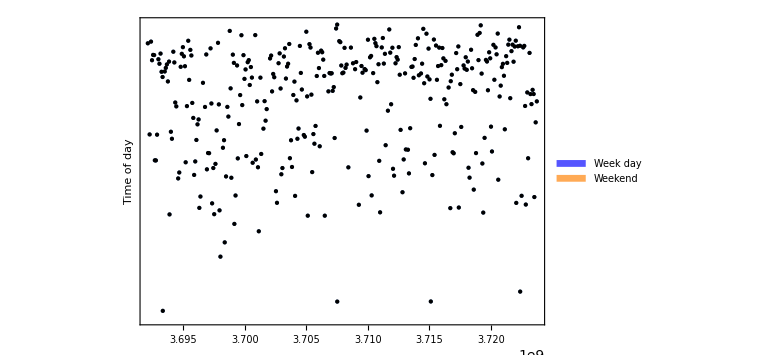

```mathematica
Legended[DateListPlot[Map[Style[#,If[DateValue[#[[1]],"ISOWeekDay"]>5,weekendColor,weekDayColor]]&,timeOfDayData],Joined->False,PlotRange->{0,24},ImageSize->Large,PlotStyle->PointSize[Large],FrameLabel->{{"Time of day",None},{None,None}},FrameTicks->{{None,All},{Automatic,None}},GridLinesStyle->Thick],SwatchLegend[{weekDayColor,weekendColor},{"Week day","Weekend"}]]
```

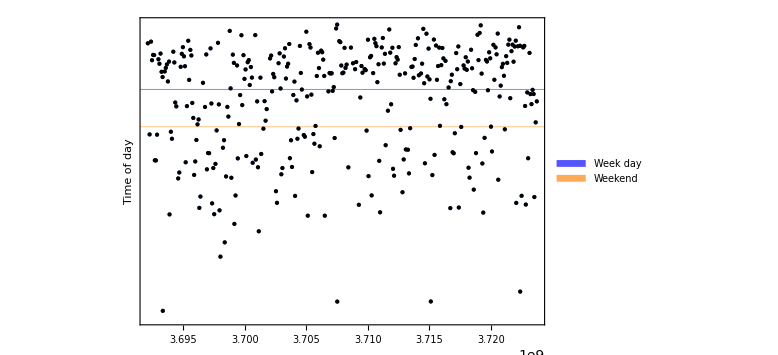

```mathematica
Legended[DateListPlot[Map[Style[#,If[DateValue[#[[1]],"ISOWeekDay"]>5,weekendColor,weekDayColor]]&,timeOfDayData],Joined->False,PlotRange->{0,24},ImageSize->Large,PlotStyle->PointSize[Large],FrameLabel->{{"Time of day",None},{None,None}},FrameTicks->{{None,All},{Automatic,None}},GridLines->{None,{{averageWeekDay,weekDayColor},{averageWeekend,weekendColor}}},GridLinesStyle->Thick],SwatchLegend[{weekDayColor,weekendColor},{"Week day","Weekend"}]]
```

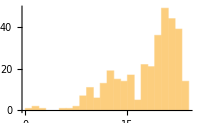
-Graphics-Time of day

```mathematica
Labeled[Histogram[timeOfDayData[[All,2]],24,Axes->{True,False},ImageSize->200],Style["Time of day",FontSize->11,FontFamily->"Roboto",FontColor->Gray]]
```